```mathematica
ClearAll;Clear[c];
```

```mathematica
(*Define the variables and parameters*)
w=1-d (1-y)^a-x (c+d g);

(*Partial derivatives*)
dwDx=D[w,x];
dwDy=D[w,y];

(*Combine derivatives with Taylor-Frank expression*)
expression=FullSimplify[dwDx+dwDy*r];

(*Display the inputs*)
{dwDx,dwDy,expression}
```

{-c-d g,a d (1-y)^(-1+a),-c-d g+a d r (1-y)^(-1+a)}

```mathematica
(*Solve for the condition where the expression is greater than 0*)
Reduce[expression>0 &&d>0&&c>0&&g>0&&r>0 &&a>0,y,Reals]
```

(0<a<1&&c>0&&d>0&&g>0&&((r>(c+d g)/(a d)&&1-((c+d g)/(a d r))^(1/(-1+a))<y<1)||(0<r≤(c+d g)/(a d)&&1-((c+d g)/(a d r))^(1/(-1+a))<y<1)))||(a==1&&c>0&&d>0&&g>0&&r>(c+d g)/d&&y<1)||(a>1&&c>0&&d>0&&g>0&&((r>(c+d g)/(a d)&&y<1-((c+d g)/(a d r))^(1/(-1+a)))||(0<r≤(c+d g)/(a d)&&y<1-((c+d g)/(a d r))^(1/(-1+a)))))

```mathematica
(* Case 1 : Diminishing function (0< a< 1; accelerating effets from immunity) *)
(0<a<1&&c>0&&d>0&&g>0&&((r>(c+d g)/(a d)&&1-((c+d g)/(a d r))^(1/(-1+a))<y<1)||(0<r≤(c+d g)/(a d)&&1-((c+d g)/(a d r))^(1/(-1+a))<y<1)))
```

```mathematica
(* Case 2 : Accelerating return (1< a; diminishing effets from immunity) *)
(a>1&&c>0&&d>0&&g>0&&((r>(c+d g)/(a d)&&y<1-((c+d g)/(a d r))^(1/(-1+a)))||(0<r≤(c+d g)/(a d)&&y<1-((c+d g)/(a d r))^(1/(-1+a)))))
```

```mathematica
(* Case 3: Reduced linear case (a= 1) *)
(a==1&&c>0&&d>0&&g>0&&r>(c+d g)/d&&y<1)
```

```mathematica
(* Solve for ESS *)
(*Reduce[expression ==0 &&d>0&&c>0&&g>0&&r>0 &&a>0 &&0<y<1,y,Reals] *)
Solve[expression ==0 ,y]
```

{{y→1-(-(-c-d g)/(a d r))^(1/(-1+a))}}

```mathematica
Reduce[expression==0 &&d>0&&c>0&&g>0&&r>0 &&1>a>0,y,Reals]
```

$Aborted

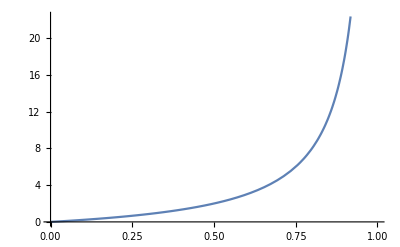

```mathematica
Plot[-c-d*g+a*d*r*(1-y)^(1-a)/. {c->1,d->1,g->1,r->1,a->2},{y,0,1}]
```